```mathematica
(*Dune Experiment
Muon neutrino to Electron Neutrino
Normal hierachy Hierachy*)
```

```mathematica
A11= Cos[θ21]Cos[θ31]
A21= Sin[θ21] Cos[θ31]
A31= Sin[θ31] Exp[-I*σ]
A32= Sin[θ31]Exp[I*σ]
B11=-(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[I*σ])
B12= -(Sin[θ21]Cos[θ32])-(Cos[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ])
B21=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[I*σ]))
B22=((Cos[θ21]Cos[θ32])-(Sin[θ21]Sin[θ32]Sin[θ31]Exp[-I*σ]))
B31=Sin[θ32]Cos[θ31]
B32=B31
δm32=δm31-δm21
Abs[δm32]<Abs[δm31]
```

Cos[θ21] Cos[θ31]

Cos[θ31] Sin[θ21]

ⅇ^(-ⅈ σ) Sin[θ31]

ⅇ^(ⅈ σ) Sin[θ31]

-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

-Cos[θ32] Sin[θ21]-ⅇ^(-ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

Cos[θ31] Sin[θ32]

-δm21+δm31

Abs[-δm21+δm31]<Abs[δm31]

```mathematica
P1=0
P2=4Re[((B22*A21*B11*A11)*(Sin[(((δm21))*(l/e)*1.27)])^2)+((B32*A31*B21*A21)*(Sin[(((δm32))*(l/e)*1.27 )])^2)+((B32*A31*B11*A11)*(Sin[(((δm31))*(l/e)*1.27)])^2)]
P3=2Im[(((B22*A21*B11*A11)Sin[(((((δm21))*(l/(2e))*1.27*4)))])+((B32*A31*B21*A21)Sin[((((δm32))*(l/(2e))*1.27*4))])+((B32*A31*B11*A11)Sin[((((δm31))*(l/(2e))*1.27*4))]))]
```

0

4 Re[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[(1.27 l δm31)/e]^2 Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(1.27 l δm21)/e]^2 Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(1.27 l (-δm21+δm31))/e]^2 Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

2 Im[ⅇ^(-ⅈ σ) Cos[θ21] Cos[θ31]^2 Sin[(2.54 l δm31)/e] Sin[θ31] Sin[θ32] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32])+Cos[θ21] Cos[θ31]^2 Sin[(2.54 l δm21)/e] Sin[θ21] (-Cos[θ32] Sin[θ21]-ⅇ^(ⅈ σ) Cos[θ21] Sin[θ31] Sin[θ32]) (Cos[θ21] Cos[θ32]-ⅇ^(-ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])+ⅇ^(-ⅈ σ) Cos[θ31]^2 Sin[(2.54 l (-δm21+δm31))/e] Sin[θ21] Sin[θ31] Sin[θ32] (Cos[θ21] Cos[θ32]-ⅇ^(ⅈ σ) Sin[θ21] Sin[θ31] Sin[θ32])]

```mathematica
probability=f[e_,σ_]=P1-P2+P3 /.{θ21->0.6021386,
θ31->0.1474803,
θ32->0.8325221,
δm21->7.56*^-5,
δm31->2.55*^-3,l->1300}
i[e_,σ_]=P1-P2+P3 /.{θ21->0.6021386,
θ31->0.1474803,
θ32->0.8325221,
δm21->7.56*^-5,
δm31->-2.55*^-3,l->1300}
```

2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.17047/e]+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.08523/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2]

2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]-0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.66973/e]]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.33487/e]^2]

```mathematica
(*i[e_,σ_]=P1-P2+P3 /.{θ21->0.6021386,
θ31->0.1467822,
θ32->0.8813913,
δm21->7.56*^-5,
δm31->-2.49*^-3,l->1300}*)
```

2 Im[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[8.22198/e]-0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[8.47161/e]]-4 Re[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[4.11099/e]^2+0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[4.23581/e]^2]

```mathematica
(*f[e_,σ_]=P1-P2+P3 /.{θ21->0.594371,
θ31->0.160875,
θ32->0.698357,
δm21->Sqrt[8*^-5],
δm32->-Sqrt[2.3*^-3],
l->1300}*)
```

Set::write: Tag Plus in (« 1 »)[e_, σ_] is Protected.

2 Im[0.456734 (0.621976-0.0545405 ⅇ^(-ⅈ σ)) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0533656 ⅇ^(-ⅈ σ) (0.621976-0.0545405 ⅇ^(ⅈ σ)) Sin[8.17047/e]+0.0776474 ⅇ^(-ⅈ σ) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[8.4201/e]]-2 Im[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[8.22198/e]-0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[8.47161/e]]-4 Re[0.456734 (0.621976-0.0545405 ⅇ^(-ⅈ σ)) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0533656 ⅇ^(-ⅈ σ) (0.621976-0.0545405 ⅇ^(ⅈ σ)) Sin[4.08523/e]^2+0.0776474 ⅇ^(-ⅈ σ) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2]+4 Re[0.456805 (0.524209-0.0639215 ⅇ^(-ⅈ σ)) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0910169 ⅇ^(-ⅈ σ) (-0.360279-0.0930063 ⅇ^(ⅈ σ)) Sin[4.11099/e]^2+0.0625542 ⅇ^(-ⅈ σ) (0.524209-0.0639215 ⅇ^(ⅈ σ)) Sin[4.23581/e]^2]

-Graphics-

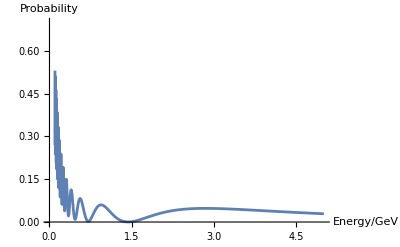

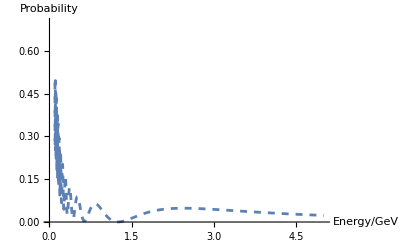

```mathematica
g1=Plot[f[e,0],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Thickness[0.005]}]
r1=Plot[i[e,0],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Dashed,Thickness[0.005]}]
```

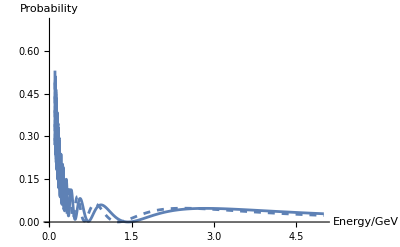

```mathematica
Show[g1,r1]
```

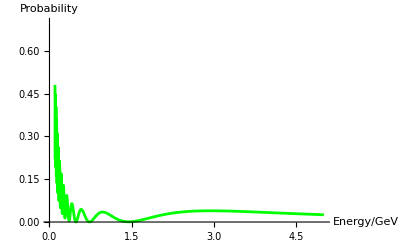

```mathematica
g2=Plot[f[e,π/4],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Green,{Thickness[0.005]}}]
```

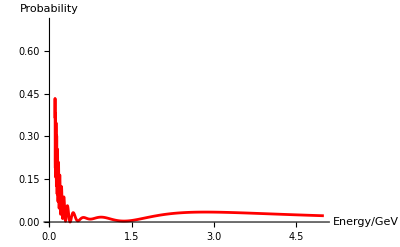

```mathematica
g3=Plot[f[e,π/2],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Red,{Thickness[0.005]}}]
```

```mathematica
(*From g2 and g3 can see that for anti neutrinos a cp phase value of (π/2) supresses and enhances the oscialltions at different energies compared with neutrinos*)
```

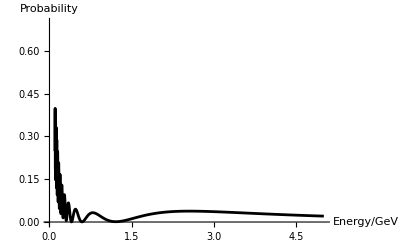

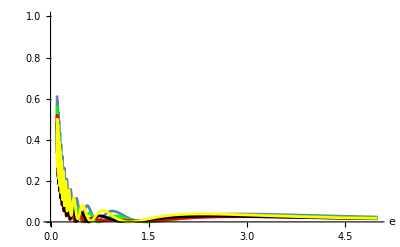

```mathematica
g4=Plot[f[e,(3π/4)],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Black,{Thickness[0.005]}}]
```

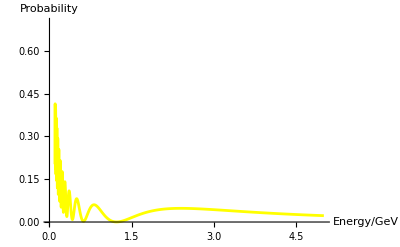

```mathematica
g5=Plot[f[e,π],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Yellow,{Thickness[0.005]}}]
```

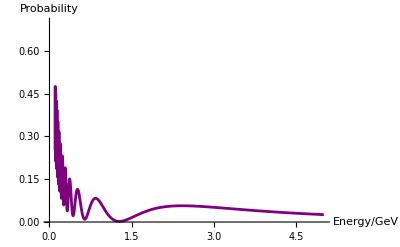

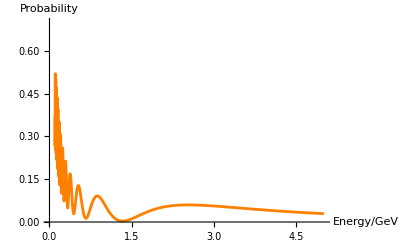

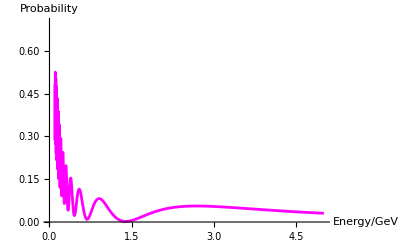

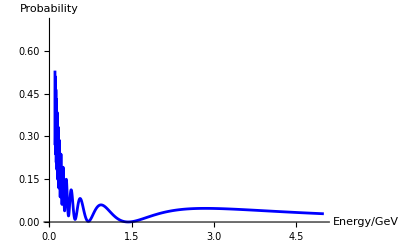

```mathematica
g6=Plot[f[e,5π/4],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Purple,{Thickness[0.005]}}]
g7=Plot[f[e,3π/2],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Orange,{Thickness[0.005]}}]
g8=Plot[f[e,7π/4],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Magenta,{Thickness[0.005]}}]
g9=Plot[f[e,2π],{e,0.1,5},PlotRange->{0,0.7},AxesLabel->{"Energy/GeV","Probability"},PlotStyle->{Blue,{Thickness[0.005]}}]
(* do g8 with cp phase 7 pi/4 and then g9 is 2pi*)
```

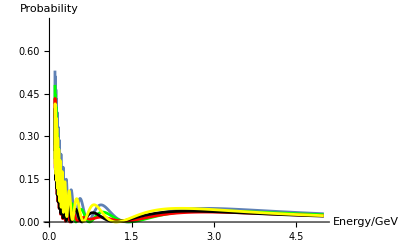

```mathematica
Show[g1,g2,g3,g4,g5]
```

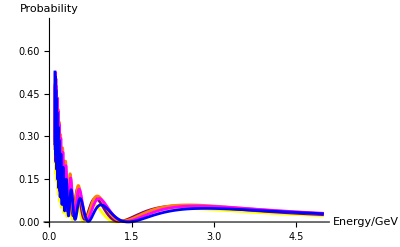

```mathematica
Show[g5,g6,g7,g8,g9]
```

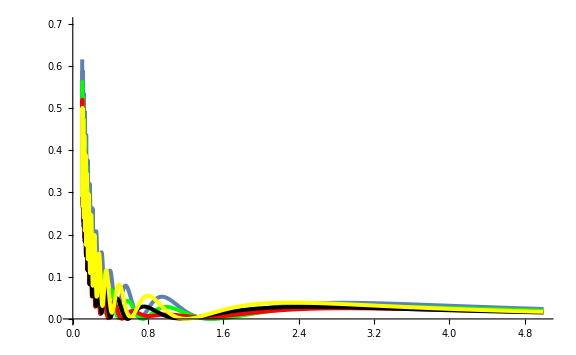

```mathematica
Show[%35,ImageSize->Large]
```

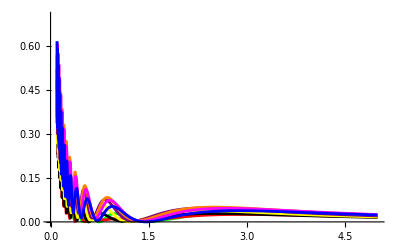

```mathematica
Show[g1,g2,g3,g4,g5,g6,g7,g8,g9]
```

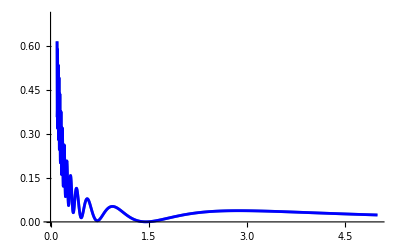

```mathematica
Show[g1,g8]
```

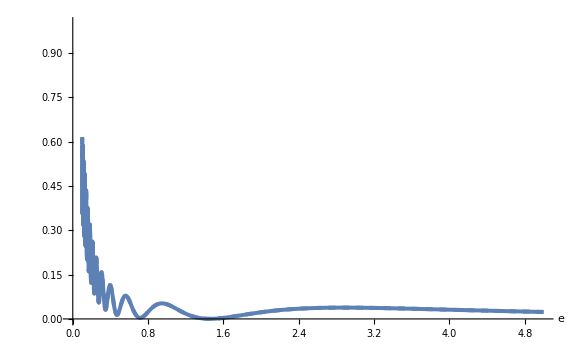

```mathematica
Show[%91,ImageSize->Large]
```

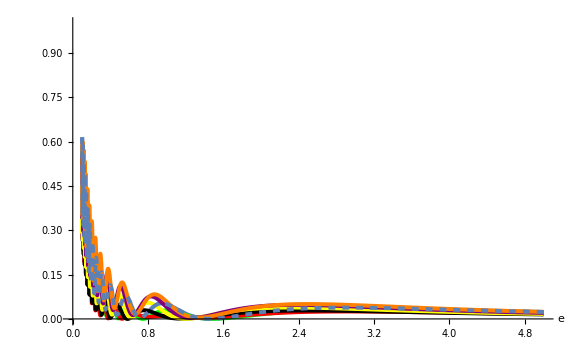

```mathematica
Show[%89,ImageSize->Large]
```

```mathematica
(*Same plot as G2 but with anti neutrinos*)
```

```mathematica
Manipulate[Plot[f[e,σ],{e,0.1,5},PlotRange->{0,1}],{σ,0,2π}]
```

```mathematica
Manipulate[Plot[g[e,σ],{e,0.1,5},PlotRange->{-1,1}],{σ,0,2π}]
```

```mathematica
(* to maximise to abilty to resolve σ despite its effect being small, then want to be able to run test a energies when Acp is as large as possible,Dunes ability to vary beam energy allows it to run tests for different cp values at energies where this asymmetry will be large and hence over many tests it should start to see this asymmetry*)
```

```mathematica
g[e_,σ_]=(f[e,σ]-f[e,-σ])/(f[e,σ]+f[e,-σ])
j[e_,σ_]=(i[e,σ]-i[e,-σ])/(i[e,σ]+i[e,-σ])
```

(-2 Im[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[8.17047/e]+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[8.4201/e]]+2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.17047/e]+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]]+4 Re[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[4.08523/e]^2+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[4.21005/e]^2]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.08523/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2])/(2 Im[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[8.17047/e]+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[8.4201/e]]+2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.17047/e]+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]]-4 Re[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[4.08523/e]^2+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[4.21005/e]^2]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.08523/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2])

(-2 Im[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[8.4201/e]-0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[8.66973/e]]+2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]-0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.66973/e]]+4 Re[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[4.21005/e]^2+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[4.33487/e]^2]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.33487/e]^2])/(2 Im[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[8.4201/e]-0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[8.66973/e]]+2 Im[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.249631/e]-0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[8.4201/e]-0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[8.66973/e]]-4 Re[0.456711 (-0.381198-0.089571 ⅇ^(-ⅈ σ)) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0876369 ⅇ^(ⅈ σ) (-0.381198-0.089571 ⅇ^(-ⅈ σ)) Sin[4.21005/e]^2+0.0602312 ⅇ^(ⅈ σ) (0.554647-0.0615604 ⅇ^(-ⅈ σ)) Sin[4.33487/e]^2]-4 Re[0.456711 (0.554647-0.0615604 ⅇ^(-ⅈ σ)) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0876369 ⅇ^(-ⅈ σ) (-0.381198-0.089571 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2+0.0602312 ⅇ^(-ⅈ σ) (0.554647-0.0615604 ⅇ^(ⅈ σ)) Sin[4.33487/e]^2])

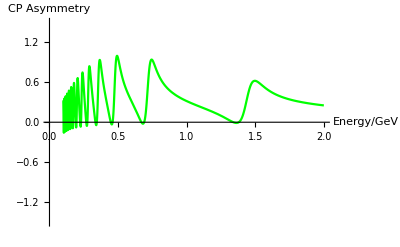

```mathematica
c1=Plot[j[e,3.80133],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Green]
```

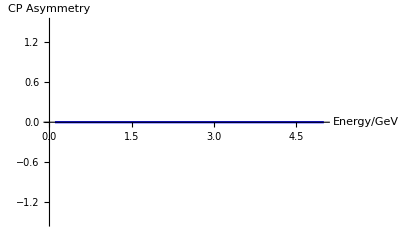

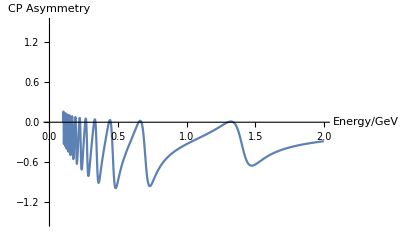

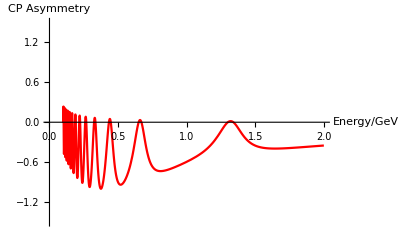

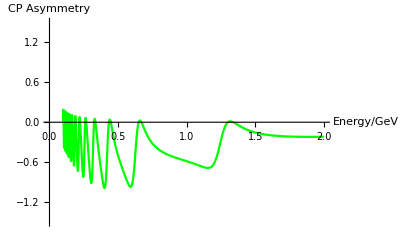

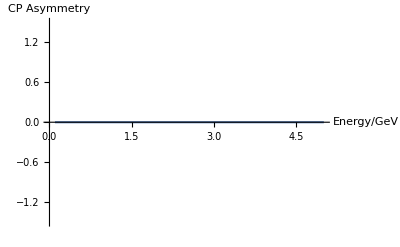

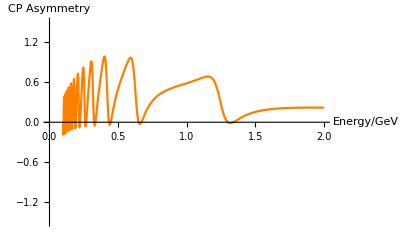

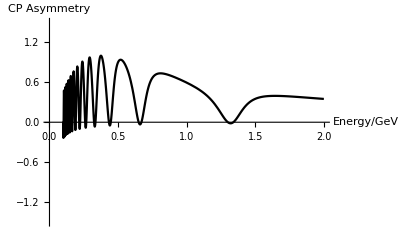

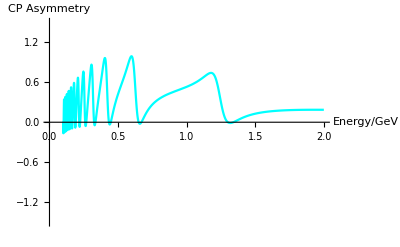

-Graphics-

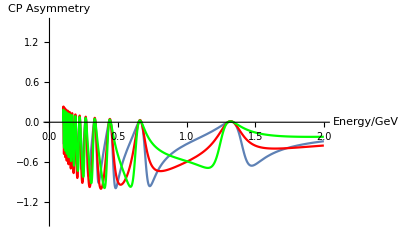

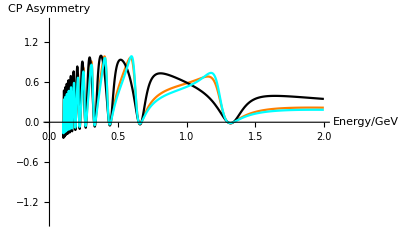

```mathematica
a1=Plot[g[e,0],{e,0.1,5},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Blue]
a2=Plot[g[e,π/4],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5}]
a3=Plot[g[e,π/2],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Red]
a4=Plot[g[e,3π/4],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Green]
a5=Plot[g[e,π],{e,0.1,5},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5}]
a6=Plot[g[e,5π/4],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Orange]
a7=Plot[g[e,3π/2],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Black]
a8=Plot[g[e,3.80133],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Cyan]
a9=Plot[g[e,2π],{e,0.1,5},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5}]

Show[a2,a3,a4]
Show[a6,a7,a8]
```

-Graphics-

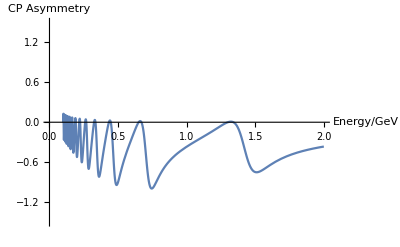

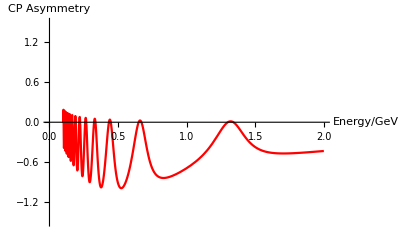

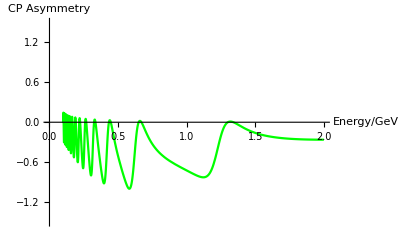

-Graphics-

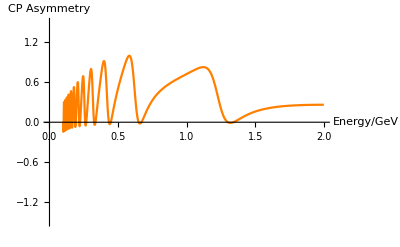

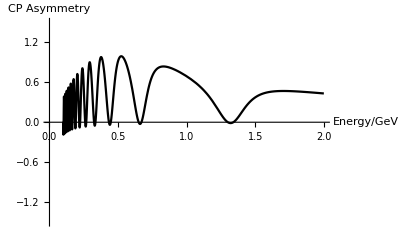

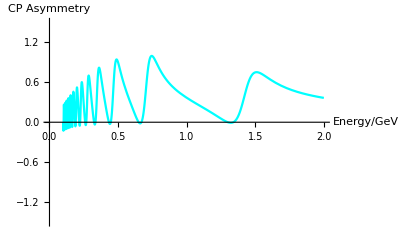

-Graphics-

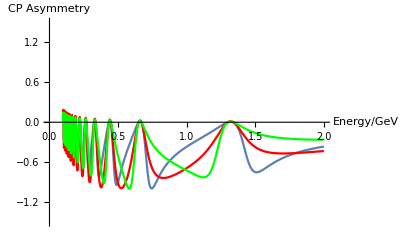

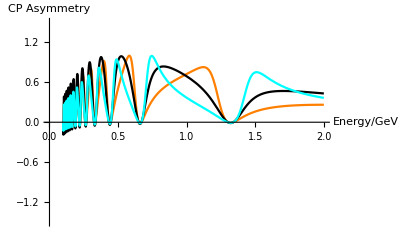

```mathematica
3.80133
```

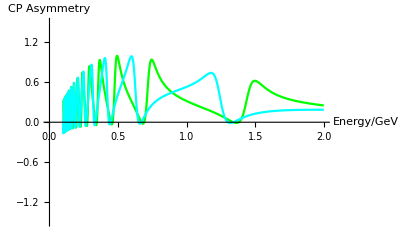

```mathematica
Show[c1,a8]
```

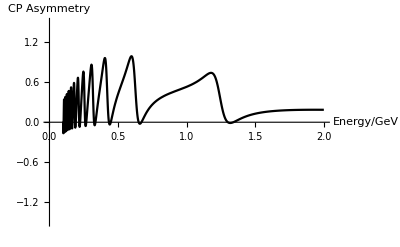

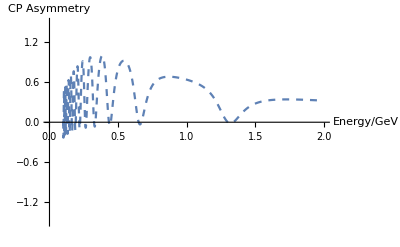

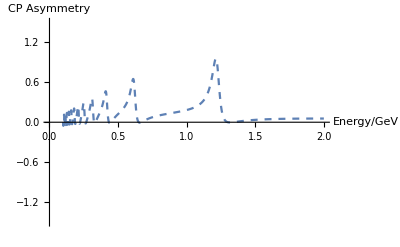

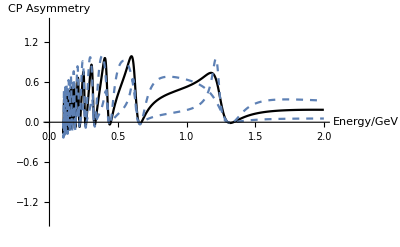

```mathematica
a10=Plot[g[e,3.80133],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Black]
a11=Plot[g[e,4.461061568],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Dashed]
a12=Plot[g[e,3.330088213],{e,0.1,2},AxesLabel->{"Energy/GeV","CP Asymmetry"},PlotRange->{-1.5,1.5},PlotStyle->Dashed]
Show[a10,a11,a12]
```

```mathematica
(*Above is graph of cp asymmetry between values of 0-2π, with a energy range of 0.1 to 10 GeV*)
```

```mathematica
(*Since effect of Cp phase is so small even at its maximum many tests will be required to narrow the range on this value for cp phase*)
```

-2 Im[0.456734 (0.621976-0.0545405 ⅇ^(-ⅈ σ)) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[0.249631/e]+0.0533656 ⅇ^(-ⅈ σ) (0.621976-0.0545405 ⅇ^(ⅈ σ)) Sin[8.17047/e]+0.0776474 ⅇ^(-ⅈ σ) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[8.4201/e]]-4 Re[0.456734 (0.621976-0.0545405 ⅇ^(-ⅈ σ)) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[0.124816/e]^2+0.0533656 ⅇ^(-ⅈ σ) (0.621976-0.0545405 ⅇ^(ⅈ σ)) Sin[4.08523/e]^2+0.0776474 ⅇ^(-ⅈ σ) (-0.427472-0.0793569 ⅇ^(ⅈ σ)) Sin[4.21005/e]^2]

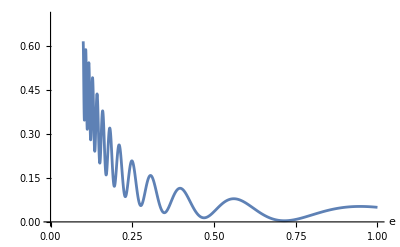

```mathematica
t[e_,σ_]=P1-P2-P3 /.{θ21->0.6021386,
θ31->0.1473058,
θ32->0.715585,
δm21->7.56*^-5,
δm31->2.55*^-3,l->1300}
Plot[t[e,0],{e,0.1,1},PlotRange->{0,0.7},AxesLabel->Automatic,PlotStyle->{Thickness[0.005]}]
```

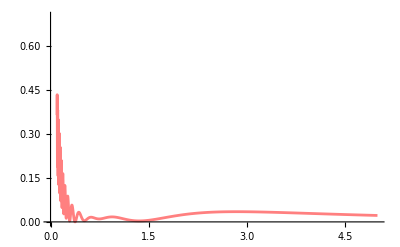

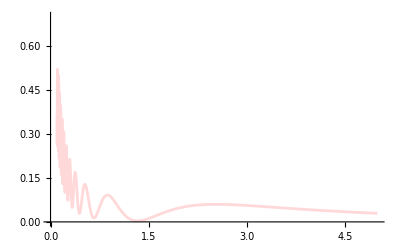

```mathematica
h1=Plot[f[e,-3π/2],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->{Pink,{Thickness[0.005]}}]
h2=Plot[f[e,-π/2],{e,0.1,5},PlotRange->{0,0.7},PlotStyle->{LightRed,{Thickness[0.005]}}]
```